# Polarization effect on dressed SPP modes in plasmonic waveguides

## Abstract:

We present the polarization effect on surface plasmonic polariton (SPP) modes in plasmonic waveguides under high-intensity radiation via the Floquet engineering methods. First, we analyze the strong light coupling to the metallic system using a nonperturbative procedure. Then, we describe the behavior of dressed metal fermion system using the Floquet state solutions. Furthermore, we examine the impurity scattering effects on electron transport in disordered plasmonic metals using the generalized Floquet-Fermi golden rule. We also show that we can reduce the SPP propagation losses in plasmonic metals by applying a dressing field. We introduce a new figure of merit (FoM) to compare the performance of popular plasmonic metals, assessing their performance enhancements under two different polarization types of dressing fields. Our study can be applied to accurately interpret the usage of strong external radiation as a tool in quantum plasmonic circuits and devices.a tool in quantum plasmonic circuits and devices.

## Import external libraries and define global parameters

```mathematica
ClearAll["Global`*"]
<<MaTeX`
Needs["CustomTicks`"];
imageScale=72/2.54;
```

## Define parameters

### Physical constants

```mathematica
e = Quantity[(1.602176)*10^(-19),"Coulombs"];  (*electron's charge*)
hbar = Quantity[(1.054571)*10^(-34),("Kilograms"*"Meters"^2)/"Seconds"]; (*Plank's constant*)
m= Quantity[(9.109383)*10^(-31),"Kilograms"]; (*electron's mass*)
c = Quantity[(2.997924)*10^(8),"Meters"/"Seconds"]; (*speed of light in vacuum*)
ϵ0 = Quantity[(8.854187)*10^(-12),("Coulombs"^2*"Seconds"^2)/("Kilograms"*"Meters"^(3))]; (*vacuum permittivity*)
eV = Quantity[(1.602176)*10^(-19),("Kilograms"*"Meters"^2)/("Seconds"^(2))];(*electron Volts*)
```

### System parameters for the dressing field

```mathematica
FieldInt0= Quantity[(20)*10^(9),"Kilograms"/"Seconds"^(3)]; (*Reference dressing electric field's intensity = 20 kWmm^-2*)
ω = Quantity[(1.35)*10^(14),"Seconds"^(-1)];(*Dressing field's frequency = 1.35×10^14 rads^-1*)
```

### System parameters for SPP trigger field

```mathematica
λspp =  Quantity[(633)*10^(-9),"Meters"]; (*SPP wave wave length*)
ωspp = (2*π*c)/λspp;(*SPP wave frequency*)
```

## Metal properties - The Drude’s model parameters

### Silver (Ag)

```mathematica
ωpSilver= 9.2; (*Plasma frequency of Ag in eV*)
ΓSilver = 0.02;(* System damping effect of Ag in eV*)
ωpSilver =Quantity[(ωpSilver *1.602176)*10^(-19),("Kilograms"*"Meters"^2)/("Seconds"^(2))]/hbar ; (*Plasma frequency*)
ΓSilver =Quantity[(ΓSilver*1.602176)*10^(-19),("Kilograms"*"Meters"^2)/("Seconds"^(2))]/hbar ; (*System natural damping constant*)
```

Dielectric function natural real part(ϵ ‘)

```mathematica
N[1 -(ωpSilver^2/(ωspp^2 +ΓSilver^2))]
```

-21.06

Dielectric function natural imaginary part(ϵ ‘’)

```mathematica
(ΓSilver*ωpSilver^2)/(ωspp*(ωspp^2 +ΓSilver^2))
```

0.225254

### Gold (Au)

```mathematica
ωpGold= 8.9; (*Plasma frequency of Au in eV*)
ΓGold = 0.07;(* System damping effect of Au in eV*)
ωpGold =Quantity[(ωpGold *1.602176)*10^(-19),("Kilograms"*"Meters"^2)/("Seconds"^(2))]/hbar ; (*Plasma frequency*)
ΓGold =Quantity[(ΓGold*1.602176)*10^(-19),("Kilograms"*"Meters"^2)/("Seconds"^(2))]/hbar ;
```

Dielectric function natural real part(ϵ ‘)

```mathematica
N[1 -(ωpGold^2/(ωspp^2 +ΓGold^2))]
```

-19.6206

Dielectric function natural imaginary part(ϵ ‘’)

```mathematica
(ΓGold*ωpGold^2)/(ωspp*(ωspp^2 +ΓGold^2))
```

0.736948

### Copper (Cu)

```mathematica
ωpCopper= 8.7; (*Plasma frequency of Cu in eV*)
ΓCopper= 0.07;(* System damping effect of Cu in eV*)
ωpCopper =Quantity[(ωpCopper *1.602176)*10^(-19),("Kilograms"*"Meters"^2)/("Seconds"^(2))]/hbar ; (*Plasma frequency*)
ΓCopper =Quantity[(ΓCopper*1.602176)*10^(-19),("Kilograms"*"Meters"^2)/("Seconds"^(2))]/hbar ; (*System natural damping constant*)
```

Dielectric function natural real part(ϵ ‘)

```mathematica
N[1 -(ωpCopper^2/(ωspp^2 +ΓCopper^2))]
```

-18.7042

Dielectric function natural imaginary part(ϵ ‘’)

```mathematica
(ΓCopper*ωpCopper^2)/(ωspp*(ωspp^2 +ΓCopper^2))
```

0.704198

### Aluminum (Al)

```mathematica
ωpAluminum= 12.7; (*Plasma frequency of Al in eV*)
ΓAluminum = 0.13;(* System damping effect of Al in eV*)
ωpAluminum =Quantity[(ωpAluminum *1.602176)*10^(-19),("Kilograms"*"Meters"^2)/("Seconds"^(2))]/hbar ;(*Plasma frequency*)
ΓAluminum =Quantity[(ΓAluminum*1.602176)*10^(-19),("Kilograms"*"Meters"^2)/("Seconds"^(2))]/hbar;  (*System natural damping constant*)
```

Dielectric function natural real part(ϵ ‘)

```mathematica
N[1 -(ωpAluminum^2/(ωspp^2 +ΓAluminum^2))]
```

-40.8575

Dielectric function natural imaginary part(ϵ ‘’)

```mathematica
(ΓAluminum*ωpAluminum^2)/(ωspp*(ωspp^2 +ΓAluminum^2))
```

2.77814

## The normalized total energy band broadening

### Ag:

```mathematica
me = 1*m;  (*Effective electron's mass for Silver = 1m *)
EFermi = 5.5*eV; (*Fermi energy for Silver = 5.5eV *)
kFermi = Sqrt[2*EFermi*me/(hbar^2)] ;(*Fermi wave number for Silver*)
Eamp =Sqrt[(2*FieldInt0)/(c*ϵ0 )];  (*Dressing electric field's amplitude*)
λ = e/(me*ω ^2); (*Pre-defined parameter*)
ξ =λ*Eamp* kFermi (*Pre-defined parameter*);
g[θ_?NumericQ,φ_?NumericQ,η_?NumericQ]:=NIntegrate[Sin[θ1]*(BesselJ[0,Sqrt[η]*ξ*(Sin[θ]Sin[φ]-Sin[θ1]Sin[φ1])])^2,{φ1,0,2π},{θ1,0,π}];
χlinear =(1/(16*π^2))*NIntegrate[(Sin[θ])*g[θ,φ,η],{φ,0,2π},{θ,0,π}];
f[φ_?NumericQ,η_?NumericQ]:=NIntegrate[Sum[Sin[φ1]*(BesselJ[m,Sqrt[η]*ξ*Sin[φ]])^2*(BesselJ[m,Sqrt[η]*ξ*Sin[φ1]])^2,{m,-10,10}],{φ1,0,π}];
χcircular =(1/4)*NIntegrate[(Sin[φ])*f[φ,η],{φ,0,π}];
```

```mathematica
SilverLinearTable = Table[χlinear ,{η,0,10,0.5}]
```

{1.,0.967239,0.936411,0.907401,0.880102,0.854412,0.830235,0.807479,0.786059,0.765894,0.746906,0.729025,0.712181,0.69631,0.681352,0.667248,0.653948,0.641398,0.629552,0.618365,0.607794}

```mathematica
SilverCircularTable = Table[χcircular ,{η,0,10,0.5}]
```

{1.,0.935138,0.875368,0.820328,0.769681,0.723111,0.680319,0.64103,0.604981,0.571931,0.541651,0.513929,0.488567,0.465379,0.444193,0.424849,0.407196,0.391095,0.376416,0.363041,0.350856}

### Au:

```mathematica
me = 1.1*m;  (*Effective electron's mass for Gold = 1.1m *)
EFermi = 5.53*eV; (*Fermi energy for Gold = 5.53eV *)
kFermi = Sqrt[2*EFermi*me/(hbar^2)] ;(*Fermi wave number for Gold*)
Eamp =Sqrt[(2*FieldInt0)/(c*ϵ0 )];  (*Dressing electric field's amplitude*)
λ = e/(me*ω ^2); (*Pre-defined parameter*)
ξ =λ*Eamp* kFermi; (*Pre-defined parameter*)
g[θ_?NumericQ,φ_?NumericQ,η_?NumericQ]:=NIntegrate[Sin[θ1]*(BesselJ[0,Sqrt[η]*ξ*(Sin[θ]Sin[φ]-Sin[θ1]Sin[φ1])])^2,{φ1,0,2π},{θ1,0,π}];
χlinear =(1/(16*π^2))*NIntegrate[(Sin[θ])*g[θ,φ,η],{φ,0,2π},{θ,0,π}];
f[φ_?NumericQ,η_?NumericQ]:=NIntegrate[Sum[Sin[φ1]*(BesselJ[m,Sqrt[η]*ξ*Sin[φ]])^2*(BesselJ[m,Sqrt[η]*ξ*Sin[φ1]])^2,{m,-10,10}],{φ1,0,π}];
χcircular =(1/4)*NIntegrate[(Sin[φ])*f[φ,η],{φ,0,π}];
```

```mathematica
GoldLinearTable = Table[χlinear ,{η,0,10,0.5}]
```

{1.,0.969977,0.941578,0.914713,0.889301,0.865262,0.84252,0.821005,0.800648,0.781386,0.763157,0.745903,0.72957,0.714106,0.699461,0.685588,0.672444,0.659986,0.648174,0.636972,0.626344}

```mathematica
GoldCircularTable = Table[χcircular ,{η,0,10,0.5}]
```

{1.,0.940508,0.885296,0.834087,0.786618,0.742644,0.701933,0.664264,0.629432,0.597243,0.567514,0.540075,0.514763,0.491427,0.469926,0.450125,0.431901,0.415136,0.399719,0.38555,0.372531}

### Cu :

```mathematica
me = 1.3*m;  (*Effective electron's mass for Copper = 1.1m *)
EFermi = 7*eV; (*Fermi energy for Copper = 5.53eV *)
kFermi = Sqrt[2*EFermi*me/(hbar^2)] ;(*Fermi wave number for Copper*)
Eamp =Sqrt[(2*FieldInt0)/(c*ϵ0 )];  (*Dressing electric field's amplitude*)
λ = e/(me*ω ^2); (*Pre-defined parameter*)
ξ =λ*Eamp* kFermi;(*Pre-defined parameter*)
g[θ_?NumericQ,φ_?NumericQ,η_?NumericQ]:=NIntegrate[Sin[θ1]*(BesselJ[0,Sqrt[η]*ξ*(Sin[θ]Sin[φ]-Sin[θ1]Sin[φ1])])^2,{φ1,0,2π},{θ1,0,π}];
χlinear =(1/(16*π^2))*NIntegrate[(Sin[θ])*g[θ,φ,η],{φ,0,2π},{θ,0,π}];
f[φ_?NumericQ,η_?NumericQ]:=NIntegrate[Sum[Sin[φ1]*(BesselJ[m,Sqrt[η]*ξ*Sin[φ]])^2*(BesselJ[m,Sqrt[η]*ξ*Sin[φ1]])^2,{m,-10,10}],{φ1,0,π}];
χcircular =(1/4)*NIntegrate[(Sin[φ])*f[φ,η],{φ,0,π}];
```

```mathematica
CopperLinearTable = Table[χlinear ,{η,0,10,0.5}]
```

{1.,0.967906,0.937667,0.909175,0.88233,0.857034,0.833198,0.810735,0.789564,0.769609,0.750796,0.733057,0.716327,0.700545,0.685654,0.671598,0.658326,0.645791,0.633946,0.622748,0.612157}

```mathematica
CopperCircularTable = Table[χcircular ,{η,0,10,0.5}]
```

{1.,0.936445,0.877778,0.823659,0.77377,0.727813,0.685508,0.64659,0.610816,0.577952,0.547785,0.52011,0.49474,0.471498,0.450218,0.430747,0.412941,0.396667,0.3818,0.368223,0.35583}

### Simulation Data Tables

```mathematica
dataIntensity = Table[x,{x,0,10,0.5}];
dataSilverLinear ={1.,0.967239,0.936411,0.907401,0.880102,0.854412,0.830235, 0.807479,0.786059,0.765894,0.746906,0.729025,0.712181,0.69631, 0.681352,0.667248,0.653948,0.641398,0.629552,0.618365,0.607794};
dataGoldLinear=  {1.,0.969977,0.941578,0.914713,0.889301,0.865262,0.84252, 0.821005,0.800648,0.781386,0.763157,0.745903,0.72957,0.714106, 0.699461,0.685588,0.672444,0.659986,0.648174,0.636972,0.626344};
dataCopperLinear =  {1.,0.967906,0.937667,0.909175,0.88233,0.857034,0.833198, 0.810735,0.789564,0.769609,0.750796,0.733057,0.716327,0.700545, 0.685654,0.671598,0.658326,0.645791,0.633946,0.622748,0.612157};
dataSilverCircular = {1.,0.935138,0.875368,0.820328,0.769681,0.723111,0.680319, 0.64103,0.604981,0.571931,0.541651,0.513929,0.488567,0.465379, 0.444193,0.424849,0.407196,0.391095,0.376416,0.363041,0.350856};
dataGoldCircular= {1.,0.940508,0.885296,0.834087,0.786618,0.742644,0.701933, 0.664264,0.629432,0.597243,0.567514,0.540075,0.514763,0.491427, 0.469926,0.450125,0.431901,0.415136,0.399719,0.38555,0.372531};
dataCopperCircular ={1.,0.936445,0.877778,0.823659,0.77377,0.727813,0.685508, 0.64659,0.610816,0.577952,0.547785,0.52011,0.49474,0.471498, 0.450218,0.430747,0.412941,0.396667,0.3818,0.368223,0.35583};
```

### Data pairs to plot the graph

```mathematica
dataSilverLinearPair = Transpose[{dataIntensity,dataSilverLinear}];
dataGoldLinearPair = Transpose[{dataIntensity,dataGoldLinear}];
dataCopperLinearPair = Transpose[{dataIntensity,dataCopperLinear}];
dataSilverCircularPair = Transpose[{dataIntensity,dataSilverCircular}];
dataGoldCircularPair = Transpose[{dataIntensity,dataGoldCircular}];
dataCopperCircularPair = Transpose[{dataIntensity,dataCopperCircular}];
```

### Comparison between linear and circular polarization effects

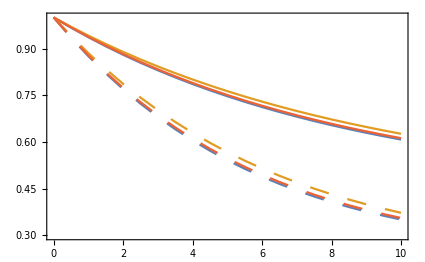

```mathematica
PSilverLinear =ListLinePlot[dataSilverLinearPair,
PlotStyle->{RGBColor[0.368417,0.506779,0.709798]},
PlotRange->{{0,10},{1,0.3}},
Axes->False,
Frame->{{True,True},{True,True}},
FrameTicksStyle->{{FontSize->22,None},{FontSize->22,None}},
FrameLabel->{{MaTeX["\\chi",FontSize->22],None},{MaTeX["\\tilde{I}",FontSize->22],None}},
LabelStyle->{{{FontFamily->"Times New Roman"},None},{FontFamily->"Times New Roman",None}},
ImageSize->15*imageScale];
PGoldLinear =ListLinePlot[dataGoldLinearPair,PlotStyle->{RGBColor[0.880722,0.611041,0.142051]}];
PCopperLinear =ListLinePlot[dataCopperLinearPair,PlotStyle->{RGBColor[0.922526,0.385626,0.209179]}];
PSilverCircular =ListLinePlot[dataSilverCircularPair,PlotStyle->{RGBColor[0.368417,0.506779,0.709798],Dashing[Large]}];
PGoldCircular =ListLinePlot[dataGoldCircularPair,PlotStyle->{RGBColor[0.880722,0.611041,0.142051],Dashing[Large]}];
PCopperCircular =ListLinePlot[dataCopperCircularPair,PlotStyle->{RGBColor[0.922526,0.385626,0.209179],Dashing[Large]}];
S3=Show[PSilverLinear,PGoldLinear,PCopperLinear,PSilverCircular,PGoldCircular,PCopperCircular];
F3 = Legended[S3,SwatchLegend[{RGBColor[0.368417,0.506779,0.709798],{RGBColor[0.880722,0.611041,0.142051]},{RGBColor[0.922526,0.385626,0.209179]}},{MaTeX["\\text{Ag}",FontSize->22],MaTeX["\\text{Au}",FontSize->22],MaTeX["\\text{Cu}",FontSize->22]}]]
```

```mathematica
Export["figure3_normalized_total_energyband_broadening_comparison.pdf",F3];
```

## SPP Characteristics

### Effects on SPP wavelength

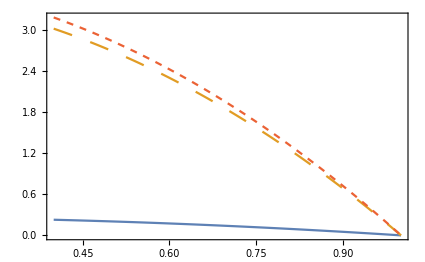

```mathematica
Λ[ωp_,Γ_,χ_] := Sqrt[(1+(1 -(ωp^2/(ωspp^2 +(χ*Γ)^2))))/((1 -(ωp^2/(ωspp^2 +(χ*Γ)^2))))];
F5= Plot[{(Λ[ωpSilver,ΓSilver,χ]-Λ[ωpSilver,ΓSilver,1])*10^5/Λ[ωpSilver,ΓSilver,1] ,
(Λ[ωpGold,ΓGold,χ]-Λ[ωpGold,ΓGold,1])*10^5/Λ[ωpGold,ΓGold,1],
(Λ[ωpCopper,ΓCopper,χ]-Λ[ωpCopper,ΓCopper,1])*10^5/Λ[ωpCopper,ΓCopper,1]},{χ,0.4,1},
MaxRecursion->0,
PlotPoints->100,
       PlotStyle->{RGBColor[0.368417,0.506779,0.709798],{RGBColor[0.880722,0.611041,0.142051],Dashing[Large]},
{RGBColor[0.922526,0.385626,0.209179],Dashing[Small]}},
Axes->False,
PlotRange->{{0.4,1},All},
Frame->{{True,True},{True,True}},
FrameTicksStyle->{{FontSize->22,None},{FontSize->22,None}},
FrameLabel->{{MaTeX["\\tilde{\\Lambda}(10^{-5})",FontSize->22],None},{MaTeX["\\chi",FontSize->22],None}},
LabelStyle->{{{FontFamily->"Times New Roman"},None},{FontFamily->"Times New Roman",None}},ImageSize->15*imageScale];
F5 =  Legended[F5,LineLegend[{RGBColor[0.368417,0.506779,0.709798],{RGBColor[0.880722,0.611041,0.142051],Dashing[Large]},
{RGBColor[0.922526,0.385626,0.209179],Dashing[Small]}},{MaTeX["\\text{Ag}",FontSize->22],MaTeX["\\text{Au}",FontSize->22],MaTeX["\\text{Cu}",FontSize->22]}]]
```

```mathematica
Export["figure5_spp_wave_analysis.pdf",F5];
```

### Effects on SPP decay lengths

#### Air Region (j=1)

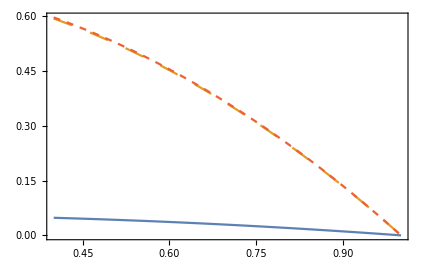

```mathematica
Δ1 [ωp_,Γ_,χ_] :=1/(Im[(π)*(Sqrt[(1)/(1 +1 -(ωp^2/(ωspp^2 +(χ*Γ)^2)))])*(2-I*(((χ*Γ*ωp^2)/(ωspp*(ωspp^2 +(χ*Γ)^2)))/(1+1 -(ωp^2/(ωspp^2 +(χ*Γ)^2)))))]);
F61= Plot[{(Δ1[ωpSilver,ΓSilver,χ]-Δ1[ωpSilver,ΓSilver,1])*10^3/Δ1[ωpSilver,ΓSilver,1] ,
(Δ1[ωpGold,ΓGold,χ]-Δ1[ωpGold,ΓGold,1])*10^3/Δ1[ωpGold,ΓGold,1],
(Δ1[ωpCopper,ΓCopper,χ]-Δ1[ωpCopper,ΓCopper,1])*10^3/Δ1[ωpCopper,ΓCopper,1]},{χ,0.4,1},
MaxRecursion->0,
PlotPoints->100,
    PlotStyle->{RGBColor[0.368417,0.506779,0.709798],{RGBColor[0.880722,0.611041,0.142051],Dashing[Large]},
{RGBColor[0.922526,0.385626,0.209179],Dashing[Small]}},
Axes->False,
PlotRange->{{0.4,1},All},
Frame->{{True,True},{True,True}},
FrameTicksStyle->{{FontSize->22,None},{FontSize->22,None}},
FrameLabel->{{MaTeX["\\tilde{\\Delta_{1}}(10^{-3})",FontSize->22],None},{MaTeX["\\chi",FontSize->22],None}},
LabelStyle->{{{FontFamily->"Times New Roman"},None},{FontFamily->"Times New Roman",None}},
ImageSize->15*imageScale];
F61=  Legended[F61,LineLegend[{RGBColor[0.368417,0.506779,0.709798],{RGBColor[0.880722,0.611041,0.142051],Dashing[Large]},
{RGBColor[0.922526,0.385626,0.209179],Dashing[Small]}},{MaTeX["\\text{Ag}",FontSize->22],MaTeX["\\text{Au}",FontSize->22],MaTeX["\\text{Cu}",FontSize->22]}]]
```

#### Metal Region (j = 2)

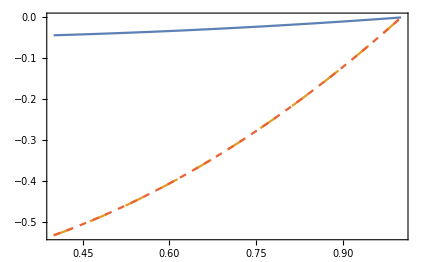

```mathematica
Δ2[ωp_,Γ_,χ_] :=1/(Im[(π)*(Sqrt[((1 -(ωp^2/(ωspp^2 +(χ*Γ)^2)))^2)/(1 +1 -(ωp^2/(ωspp^2 +(χ*Γ)^2)))])*(2+I*(((χ*Γ*ωp^2)/(ωspp*(ωspp^2 +(χ*Γ)^2)))/(1 -(ωp^2/(ωspp^2 +(χ*Γ)^2)))))]);
F62= Plot[{(Δ2[ωpSilver,ΓSilver,χ]-Δ2[ωpSilver,ΓSilver,1])*10^3/Δ2[ωpSilver,ΓSilver,1] ,
(Δ2[ωpGold,ΓGold,χ]-Δ2[ωpGold,ΓGold,1])*10^3/Δ2[ωpGold,ΓGold,1],
(Δ2[ωpCopper,ΓCopper,χ]-Δ2[ωpCopper,ΓCopper,1])*10^3/Δ2[ωpCopper,ΓCopper,1]},{χ,0.4,1},
MaxRecursion->0,
PlotPoints->100,
     PlotStyle->{RGBColor[0.368417,0.506779,0.709798],{RGBColor[0.880722,0.611041,0.142051],Dashing[Large]},
{RGBColor[0.922526,0.385626,0.209179],Dashing[Small]}},
Axes->False,
PlotRange->{{0.4,1},All},
Frame->{{True,True},{True,True}},
FrameTicksStyle->{{FontSize->22,None},{FontSize->22,None}},
FrameLabel->{{MaTeX["\\tilde{\\Delta_{2}}(10^{-3})",FontSize->22],None},{MaTeX["\\chi",FontSize->22],None}},
LabelStyle->{{{FontFamily->"Times New Roman"},None},{FontFamily->"Times New Roman",None}},
ImageSize->15*imageScale];
F62 = Legended[F62,LineLegend[{RGBColor[0.368417,0.506779,0.709798],{RGBColor[0.880722,0.611041,0.142051],Dashing[Large]},
{RGBColor[0.922526,0.385626,0.209179],Dashing[Small]}},{MaTeX["\\text{Ag}",FontSize->22],MaTeX["\\text{Au}",FontSize->22],MaTeX["\\text{Cu}",FontSize->22]}]]
```

```mathematica
Export["figure6_decay_length_1.pdf",F61];
Export["figure6_decay_length_2.pdf",F62];
```

### Effects on SPP propagation length

```mathematica
L[ωp_,Γ_,χ_]:=(1/(2π))*(Sqrt[(1+1-(ωp^2/(ωspp^2+(Γ*χ)^2)))/(1-(ωp^2/(ωspp^2+(Γ*χ)^2)))])*(((1-(ωp^2/(ωspp^2+(Γ*χ)^2)))* (1+1-(ωp^2/(ωspp^2+(Γ*χ)^2))))/(Γ*χ*ωp^2/(ωspp*(ωspp^2+(Γ*χ)^2)) ));
```

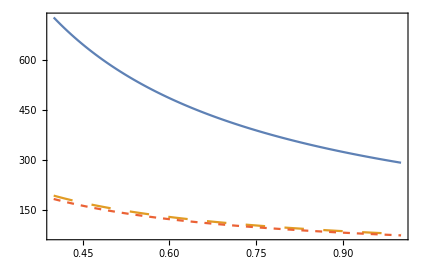

```mathematica
F70= Plot[{L[ωpSilver,ΓSilver,χ],
L[ωpGold,ΓGold,χ],
L[ωpCopper,ΓCopper,χ]},{χ,0.4,1},
MaxRecursion->0,
PlotPoints->100,
     PlotStyle->{RGBColor[0.368417,0.506779,0.709798],{RGBColor[0.880722,0.611041,0.142051],Dashing[Large]},
{RGBColor[0.922526,0.385626,0.209179],Dashing[Small]}},
Axes->False,
PlotRange->{{0.4,1},All},
Frame->{{True,True},{True,True}},
FrameTicksStyle->{{FontSize->22,None},{FontSize->22,None}},
FrameLabel->{{MaTeX["\\mathcal{L}",FontSize->22],None},{MaTeX["\\chi",FontSize->22],None}},
LabelStyle->{{{FontFamily->"Times New Roman"},None},{FontFamily->"Times New Roman",None}},
ImageSize->15*imageScale];
F70 = Legended[F70,LineLegend[{RGBColor[0.368417,0.506779,0.709798],{RGBColor[0.880722,0.611041,0.142051],Dashing[Large]},
{RGBColor[0.922526,0.385626,0.209179],Dashing[Small]}},{MaTeX["\\text{Ag}",FontSize->22],MaTeX["\\text{Au}",FontSize->22],MaTeX["\\text{Cu}",FontSize->22]}]]
```

```mathematica
Export["figure7_propagation_length.pdf",F70];
```

```mathematica
dataSilverLinearFrom1 = { 0.936411,0.907401,0.880102,0.854412,0.830235, 0.807479,0.786059,0.765894,0.746906,0.729025,0.712181,0.69631, 0.681352,0.667248,0.653948,0.641398,0.629552,0.618365,0.607794};
dataGoldLinearFrom1= {0.941578,0.914713,0.889301,0.865262,0.84252, 0.821005,0.800648,0.781386,0.763157,0.745903,0.72957,0.714106, 0.699461,0.685588,0.672444,0.659986,0.648174,0.636972,0.626344};
dataCopperLinearFrom1 = {0.937667,0.909175,0.88233,0.857034,0.833198, 0.810735,0.789564,0.769609,0.750796,0.733057,0.716327,0.700545, 0.685654,0.671598,0.658326,0.645791,0.633946,0.622748,0.612157};
dataSilverCircularFrom1 ={0.875368,0.820328,0.769681,0.723111,0.680319, 0.64103,0.604981,0.571931,0.541651,0.513929,0.488567,0.465379, 0.444193,0.424849,0.407196,0.391095,0.376416,0.363041,0.350856};
dataGoldCircularFrom1={0.885296,0.834087,0.786618,0.742644,0.701933, 0.664264,0.629432,0.597243,0.567514,0.540075,0.514763,0.491427, 0.469926,0.450125,0.431901,0.415136,0.399719,0.38555,0.372531} ;
dataCopperCircularFrom1 = {0.877778,0.823659,0.77377,0.727813,0.685508, 0.64659,0.610816,0.577952,0.547785,0.52011,0.49474,0.471498, 0.450218,0.430747,0.412941,0.396667,0.3818,0.368223,0.35583};
```

```mathematica
Evaluate natural normalized propagation length
```

Evaluate length natural normalized propagation

```mathematica
L0Silver =L[ωpSilver,ΓSilver,1]
L0Gold =L[ωpGold,ΓGold,1]
L0Copper=L[ωpCopper,ΓCopper,1]
```

291.322

76.8651

72.8132

#### Calculate normalized propagation length difference

```mathematica
qI=Table[x,{x,1,10,0.5}];
```

```mathematica
qSilverNormLinear=(L[ωpSilver,ΓSilver,dataSilverLinearFrom1]-L0Silver)/L0Silver;
dataSilverWithIntensityNormLinear = Transpose[{qI,qSilverNormLinear}];
qSilverNormCircular=(L[ωpSilver,ΓSilver,dataSilverCircularFrom1]-L0Silver)/L0Silver;
dataSilverWithIntensityNormCircular= Transpose[{qI,qSilverNormCircular}];
```

```mathematica
qGoldNormLinear=(L[ωpGold,ΓGold,dataGoldLinearFrom1]-L0Gold)/L0Gold;
dataGoldWithIntensityNormLinear = Transpose[{qI,qGoldNormLinear}];
qGoldNormCircular=(L[ωpGold,ΓGold,dataGoldCircularFrom1]-L0Gold)/L0Gold;
dataGoldWithIntensityNormCircular= Transpose[{qI,qGoldNormCircular}];
```

```mathematica
qCopperNormLinear=(L[ωpCopper,ΓCopper,dataCopperLinearFrom1]-L0Copper)/L0Copper;
dataCopperWithIntensityNormLinear = Transpose[{qI,qCopperNormLinear}];
qCopperNormCircular=(L[ωpCopper,ΓCopper,dataCopperCircularFrom1]-L0Copper)/L0Copper;
dataCopperWithIntensityNormCircular= Transpose[{qI,qCopperNormCircular}];
```

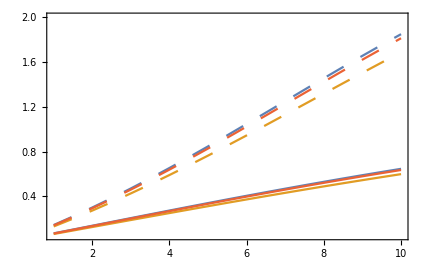

```mathematica
PSilverIntNorm =ListLinePlot[dataSilverWithIntensityNormLinear,
PlotStyle->{RGBColor[0.368417,0.506779,0.709798]},
PlotRange->{{1,10},{0.05, 2}},
Axes->False,
Frame->{{True,True},{True,True}},
FrameTicksStyle->{{FontSize->22,None},{FontSize->22,None}},
FrameLabel->{{MaTeX["\\tilde{\\mathcal{L}}",FontSize->22],None},{MaTeX["\\tilde{I}",FontSize->22],None}},
LabelStyle->{{{FontFamily->"Times New Roman"},None},{FontFamily->"Times New Roman",None}},
ImageSize->15*imageScale];
PGoldIntNorm =ListLinePlot[dataGoldWithIntensityNormLinear,PlotStyle->{RGBColor[0.880722,0.611041,0.142051]}];
PCopperIntNorm =ListLinePlot[dataCopperWithIntensityNormLinear,PlotStyle->{RGBColor[0.922526,0.385626,0.209179]}];
PSilverIntNormC =ListLinePlot[dataSilverWithIntensityNormCircular,PlotStyle->{RGBColor[0.368417,0.506779,0.709798],Dashing[Large]}];
PGoldIntNormC =ListLinePlot[dataGoldWithIntensityNormCircular,PlotStyle->{RGBColor[0.880722,0.611041,0.142051],Dashing[Large]}];
PCopperIntNormC =ListLinePlot[dataCopperWithIntensityNormCircular,PlotStyle->{RGBColor[0.922526,0.385626,0.209179],Dashing[Large]}];
S7=Show[PSilverIntNorm,PGoldIntNorm,PCopperIntNorm,PSilverIntNormC,PGoldIntNormC,PCopperIntNormC];
F7= Legended[S7,SwatchLegend[{RGBColor[0.368417,0.506779,0.709798],{RGBColor[0.880722,0.611041,0.142051],Dashing[Large]},{RGBColor[0.922526,0.385626,0.209179],Dashing[Medium]}},{MaTeX["\\text{Ag}",FontSize->22],MaTeX["\\text{Au}",FontSize->22],MaTeX["\\text{Cu}",FontSize->22]}]]
```

```mathematica
Export["figure7_normalized_propagation_length.pdf",F7];
```

## Figure of Merit

### Normalized inverse scattering time for I=I0 and I=4*I0 intensity levels:

```mathematica
χ1SilverLinear =0.9364 ;
χ8SilverLinear = 0.6539;
χ1GoldLinear= 0.9416;
χ8GoldLinear= 0.6724;
χ1CopperLinear= 0.9377;
χ8CopperLinear = 0.6583;
```

```mathematica
χ1SilverCircular=0.8754 ;
χ8SilverCircular = 0.4072;
χ1GoldCircular= 0.8853;
χ8GoldCircular= 0.4319;
χ1CopperCircular= 0.8778;
χ8CopperCircular = 0.4129;
```

#### Silver normalized values - linear

```mathematica
χISilverLinear = χ8SilverLinear;
LNormSilverLinear = (L[ωpSilver,ΓSilver,χISilverLinear]-L0Silver)/L0Silver
Δ1NormSilverLinear = (Δ1[ωpSilver,ΓSilver,χISilverLinear]-Δ1[ωpSilver,ΓSilver,1])*10^3/Δ1[ωpSilver,ΓSilver,1]
Δ2NormSilverLinear = (Δ2[ωpSilver,ΓSilver,χISilverLinear]-Δ2[ωpSilver,ΓSilver,1])*10^3/Δ2[ωpSilver,ΓSilver,1] 
ΛNormSilverLinear =(Λ[ωpSilver,ΓSilver,χISilverLinear]-Λ[ωpSilver,ΓSilver,1])*10^5/Λ[ωpSilver,ΓSilver,1]
```

0.529393

0.0328144

-0.0296973

0.155806

#### Silver normalized values - circular

```mathematica
χISilverCircular= χ8SilverCircular;
LNormSilverCircular = (L[ωpSilver,ΓSilver,χISilverCircular]-L0Silver)/L0Silver
Δ1NormSilverCircular = (Δ1[ωpSilver,ΓSilver,χISilverCircular]-Δ1[ωpSilver,ΓSilver,1])*10^3/Δ1[ωpSilver,ΓSilver,1]
Δ2NormSilverCircular = (Δ2[ωpSilver,ΓSilver,χISilverCircular]-Δ2[ωpSilver,ΓSilver,1])*10^3/Δ2[ωpSilver,ΓSilver,1] 
ΛNormSilverCircular =(Λ[ωpSilver,ΓSilver,χISilverCircular]-Λ[ωpSilver,ΓSilver,1])*10^5/Λ[ωpSilver,ΓSilver,1]
```

1.45605

0.0478218

-0.0432786

0.227059

#### Gold normalized values - linear

```mathematica
χIGoldLinear = χ8GoldLinear ;
LNormGoldLinear = (L[ωpGold,ΓGold,χIGoldLinear]-L0Gold)/L0Gold
Δ1NormGoldLinear = (Δ1[ωpGold,ΓGold,χIGoldLinear]-Δ1[ωpGold,ΓGold,1])*10^3/Δ1[ωpGold,ΓGold,1]
Δ2NormGoldLinear= (Δ2[ωpGold,ΓGold,χIGoldLinear]-Δ2[ωpGold,ΓGold,1])*10^3/Δ2[ωpGold,ΓGold,1] 
ΛNormGoldLinear =(Λ[ωpGold,ΓGold,χIGoldLinear]-Λ[ωpGold,ΓGold,1])*10^5/Λ[ωpGold,ΓGold,1]
```

0.488444

0.387167

-0.347588

1.97218

#### Gold normalized values - circular

```mathematica
χIGoldCircular= χ8GoldCircular;
LNormGoldCircular = (L[ωpGold,ΓGold,χIGoldCircular]-L0Gold)/L0Gold
Δ1NormGoldCircular = (Δ1[ωpGold,ΓGold,χIGoldCircular]-Δ1[ωpGold,ΓGold,1])*10^3/Δ1[ωpGold,ΓGold,1]
Δ2NormGoldCircular= (Δ2[ωpGold,ΓGold,χIGoldCircular]-Δ2[ωpGold,ΓGold,1])*10^3/Δ2[ωpGold,ΓGold,1] 
ΛNormGoldCircular =(Λ[ωpGold,ΓGold,χIGoldCircular]-Λ[ωpGold,ΓGold,1])*10^5/Λ[ωpGold,ΓGold,1]
```

1.3182

0.574987

-0.516127

2.92813

#### Copper normalized values - linear

```mathematica
χICopperLinear  =χ8CopperLinear ;
LNormCopperLinear = (L[ωpCopper,ΓCopper,χICopperLinear ]-L0Copper)/L0Copper
Δ1NormCopperLinear = (Δ1[ωpCopper,ΓCopper,χICopperLinear ]-Δ1[ωpCopper,ΓCopper,1])*10^3/Δ1[ωpCopper,ΓCopper,1]
Δ2NormCopperLinear = (Δ2[ωpCopper,ΓCopper,χICopperLinear ]-Δ2[ωpCopper,ΓCopper,1])*10^3/Δ2[ωpCopper,ΓCopper,1] 
ΛNormCopperLinear =(Λ[ωpCopper,ΓCopper,χICopperLinear ]-Λ[ωpCopper,ΓCopper,1])*10^5/Λ[ωpCopper,ΓCopper,1]
```

0.520379

0.402443

-0.35929

2.15039

#### Copper normalized values - circular

```mathematica
χICopperCircular =χ8CopperCircular;
LNormCopperCircular= (L[ωpCopper,ΓCopper,χICopperCircular]-L0Copper)/L0Copper
Δ1NormCopperCircular= (Δ1[ωpCopper,ΓCopper,χICopperCircular]-Δ1[ωpCopper,ΓCopper,1])*10^3/Δ1[ωpCopper,ΓCopper,1]
Δ2NormCopperCircular= (Δ2[ωpCopper,ΓCopper,χICopperCircular]-Δ2[ωpCopper,ΓCopper,1])*10^3/Δ2[ωpCopper,ΓCopper,1] 
ΛNormCopperCircular=(Λ[ωpCopper,ΓCopper,χICopperCircular]-Λ[ωpCopper,ΓCopper,1])*10^5/Λ[ωpCopper,ΓCopper,1]
```

1.42496

0.589284

-0.526015

3.14791

### FoM Values (I=1 or I=8) - linear

```mathematica
FoMSilverLinear=NumberForm[LNormSilverLinear*Abs[Δ2NormSilverLinear]/(Δ1NormSilverLinear*Abs[ΛNormSilverLinear]),{5,4}]
FoMGoldLinear=NumberForm[LNormGoldLinear*Abs[Δ2NormGoldLinear]/(Δ1NormGoldLinear*Abs[ΛNormGoldLinear]),{5,4}]
FoMCopperLinear=NumberForm[LNormCopperLinear*Abs[Δ2NormCopperLinear]/(Δ1NormCopperLinear*Abs[ΛNormCopperLinear]),{5,4}]
```

3.0750

0.2223

0.2160

### FoM Values (I=1 or I=8) - circular

```mathematica
FoMSilverCircular=NumberForm[LNormSilverCircular*Abs[Δ2NormSilverCircular]/(Δ1NormSilverCircular*Abs[ΛNormSilverCircular]),{5,4}]
FoMGoldCircular=NumberForm[LNormGoldCircular*Abs[Δ2NormGoldCircular]/(Δ1NormGoldCircular*Abs[ΛNormGoldCircular]),{5,4}]
FoMCopperCircular=NumberForm[LNormCopperCircular*Abs[Δ2NormCopperCircular]/(Δ1NormCopperCircular*Abs[ΛNormCopperCircular]),{5,4}]
```

5.8034

0.4041

0.4041